```mathematica
SetDirectory["/Users/marcelo/Documents/UH/ME 360/Jupyter/lectures/interpolating-polynomial/saturated-liquid"]
```

/Users/marcelo/Documents/UH/ME 360/Jupyter/lectures/interpolating-polynomial/saturated-liquid

```mathematica
data=Import["saturated-liquid-table.csv"];
data=Drop[data,1];
x0=data[[1,1]];
x1=data[[-1,1]];
```

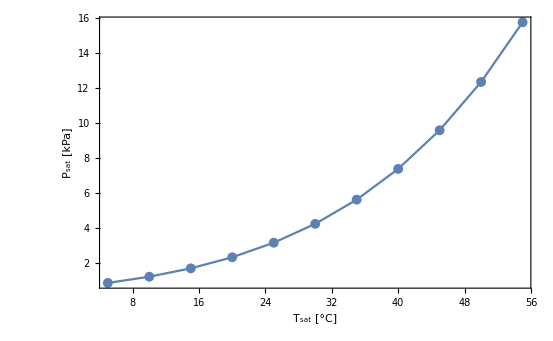

```mathematica
sL[x_]=Interpolation[data,x,Method->"Spline",InterpolationOrder->1];
sC[x_]=Interpolation[data,x,Method->"Spline",InterpolationOrder->3];
pN[x_]=InterpolatingPolynomial[data,x];
Show[ListPlot[data],Plot[{sL[x]},{x,x0,x1}],PlotRange->All,Frame->True,FrameLabel->{"T_sat [°C]","P_sat [kPa]"}]
```